DMI on top and bottom surfaces are equal here.

One may therefore expect the DMI to not change the spin wave frequencies because D_eff=0. But it does!
Final data is at the end. We also played with the analytic expression for the frequency of the uniform mode here.

## The Eigenfrequencies -- D==0. N=16 (restart kernel)

#### Some parameters needed for the code

```mathematica
B=0.03;
Δ=1;
Φ[0]=Table[0,{4}];
```

```mathematica
LL=16;
```

```mathematica
a=0.248 10^-9;  (*0.25 nm atomic spacing*)
Ms=835563; (*A/m*)
AA=1.355 10^-11;  (*J/m*)
DD =0.0 4.2 10^-3 1/1; (* i.e. This is 4.2 mJ/m^2 for 1 layer and decreases for thicker films!*)
JJ=(2 AA)/(a^2 Ms)
```

527.335

```mathematica
K[i_]:=K[i]=Which[i<LL/2+0.5,0,i>LL/2+0.5,0]
J[i_]:=J[i]=Which[i<LL/2+0.5,JJ,i>LL/2+0.5,JJ]
H[i_]:=H[i]=Which[i<LL/2+0.5,B,i>LL/2+0.5,B]
HDMI[1]=2 DD/(a Ms);
HDMI[LL]=-2 DD/(a Ms);
```

0

```mathematica
ϕ[i_]:=ϕ[i]=0
```

#### Coding required to create dynamical matrix

For a typical plane of spins in the wall the code is:

```mathematica
acomponent[i_,y_,z_]:=acomponent[i,y,z]=H[i] Cos[ϕ[i]]+(4 π 10^-7) Ms+2 K[i] (Cos[ϕ[i]]^2-Sin[ϕ[i]]^2)+J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])+4 J[i]-2 J[i] Cos[y]-2 J[i] Cos[z]
aplus[i_]:=aplus[i]=-J[i] Cos[ϕ[i]-ϕ[i+1]]
aminus[i_]:=aminus[i]=-J[i] Cos[ϕ[i]-ϕ[i-1]]
bcomponent[i_,y_,z_]:=bcomponent[i,y,z]=-H[i] Cos[ϕ[i]]-2 K[i] Cos[ϕ[i]]^2-J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])-4 J[i]+2 J[i] Cos[y]+2 J[i] Cos[z]
```

```mathematica
rowa[NN_,k_,y_,z_]:=Join[Table[0,{2 k-3}],{aminus[k],0,acomponent[k,y,z],0,aplus[k]},Table[0,{2 NN-2-2 k}]]
rowb[NN_,k_,y_,z_]:=Join[Table[0,{2 k-4}],{J[k],0,bcomponent[k,y,z],0,J[k]},Table[0,{2 NN-1-2 k}]]
```

The 1st, (N/2)th, (N/2 +1)th and Nth planes all need individual codes sinse they have different exchange coupling to the planes on either side.
The codes are as follows:

```mathematica
arow1[NN_,y_,z_]:=arow1[NN,y,z]=Join[
{-HDMI[1] Sin[y] ⅈ,
H[1] Cos[ϕ[1]]+(4 π 10^-7) Ms+2 K[1] (Cos[ϕ[1]]^2-Sin[ϕ[1]]^2)+J[1] (0+Cos[ϕ[1]-ϕ[2]])+4 J[1]-2 J[1] Cos[y]-2 J[1] Cos[z],
0,
aplus[1]},
Table[0,{2 NN-4}]];
```

```mathematica
brow1[NN_,y_,z_]:=brow1[NN,y,z]=Join[
{-H[1] Cos[ϕ[1]]-2 K[1] Cos[ϕ[1]]^2-J[1] (0+Cos[ϕ[1]-ϕ[2]])-4 J[1]+2 J[1] Cos[y]+2 J[1] Cos[z],
-HDMI[1] Sin[y] ⅈ,
J[2]},
Table[0,{2 NN-3}]];
```

Note that I have kept the ANGULAR dependence in this code, which was set up for dealing with an exchange spring. It is not needed here, but it is an interesting question to see how the DMI can change the modes on an exchange spring...

```mathematica
arow50[NN_,y_,z_,β_]:=arow50[NN,y,z,β]=Join[
Table[0,{NN -3}],
{aminus[NN/2],
0,
H[NN/2] Cos[ϕ[NN/2]]+(4 π 10^-7) Ms+2 K[NN/2] (Cos[ϕ[NN/2]]^2-Sin[ϕ[NN/2]]^2)+J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2]]+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]+4 J[NN/2]-2 J[NN/2] Cos[y]-2 J[NN/2] Cos[z],
0,
-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]},
Table[0,{NN-2}]]
```

```mathematica
brow50[NN_,y_,z_,β_]:=brow50[NN,y,z,β]=Join[
Table[0,{NN-4}],
{J[NN/2],
0,
-H[NN/2] Cos[ϕ[NN/2]]-2 K[NN/2] Cos[ϕ[NN/2]]^2-J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2-1]]-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]-4 J[NN/2]+2 J[NN/2] Cos[y]+2 J[NN/2] Cos[z],
0,
J[NN]+β (J[1]-J[NN])},
Table[0,{NN-1}]]
```

```mathematica
arow51[NN_,y_,z_,β_]:=arow51[NN,y,z,β]=Join[
Table[0,{NN-1}],
{-(J[NN/2]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]],
0,
H[NN/2+1] Cos[ϕ[NN/2+1]]+(4 π 10^-7) Ms+2 K[NN/2+1] (Cos[ϕ[NN/2+1]]^2-Sin[ϕ[NN/2+1]]^2)+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]+J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]+4 J[NN/2+1]-2 J[NN/2+1] Cos[y]-2 J[NN/2+1] Cos[z],
0,
aplus[NN/2+1]},
Table[0,{NN-4}]]
```

```mathematica
brow51[NN_,y_,z_,β_]:=brow51[NN,y,z,β]=Join[
Table[0,{NN-2}],
{J[NN]+β (J[1]-J[NN]),
0,
-H[NN/2+1] Cos[ϕ[NN/2+1]]-2 K[NN/2+1] Cos[ϕ[NN/2+1]]^2-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]-J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]-4 J[NN/2+1]+2 J[NN/2+1] Cos[y]+2 J[NN/2+1] Cos[z],
0,
J[NN/2+1]},
Table[0,{NN-3}]]
```

```mathematica
arow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-3}],
{aminus[NN],
-HDMI[NN] Sin[y] ⅈ,
H[NN] Cos[ϕ[NN]]+(4 π 10^-7) Ms+2 K[NN] (Cos[ϕ[NN]]^2-Sin[ϕ[NN]]^2)+J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)+4 J[NN]-2 J[NN] Cos[y]-2 J[NN] Cos[z]}];
```

```mathematica
brow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-4}],
{J[NN-1],
0,
-H[NN] Cos[ϕ[NN]]-2 K[NN] Cos[ϕ[NN]]^2-J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)-4 J[NN]+2 J[NN] Cos[y]+2 J[NN] Cos[z],
-HDMI[NN] Sin[y] ⅈ}];
```

#### The dynamical matrix and eigenfrequencies

The dynamical matrix is:

```mathematica
big[NN_,y_,z_,β_]:=big[NN,y,z,β]=Join[
{arow1[NN,y,z],brow1[NN,y,z]},
Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,2,NN/2-1}],1],{arow50[NN,y,z,β],brow50[NN,y,z,β],arow51[NN,y,z,β],brow51[NN,y,z,β]},Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,NN/2+2,NN-1}],1],
{arow100[NN,y,z],brow100[NN,y,z]}]
```

The eigenfrequencies are given by (γ = 176 GHz rad/T):

```mathematica
freqs[NN_,y_,z_,β_]:=freqs[NN,y,z,β]=176/(2. π)Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,2}]
```

```mathematica
freqs2[NN_,y_,z_,β_]:=freqs2[NN,y,z,β]=176/(2. π) Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,1}]
```

## The Eigenfrequencies -- D = 9 mJ/m^2 on top and bottom. N=16 (restart kernel)

#### Some parameters needed for the code

```mathematica
B=0.03;
Δ=1;
Φ[0]=Table[0,{4}];
```

```mathematica
LL=16;
```

```mathematica
a=0.248 10^-9;  (*0.25 nm atomic spacing*)
Ms=835563; (*A/m*)
AA=1.355 10^-11;  (*J/m*)
DD =9 10^-3 1/1; (* i.e. This is 4.2 mJ/m^2 for 1 layer and decreases for thicker films!*)
JJ=(2 AA)/(a^2 Ms)
```

527.335

```mathematica
K[i_]:=K[i]=Which[i<LL/2+0.5,0,i>LL/2+0.5,0]
J[i_]:=J[i]=Which[i<LL/2+0.5,JJ,i>LL/2+0.5,JJ]
H[i_]:=H[i]=Which[i<LL/2+0.5,B,i>LL/2+0.5,B]
HDMI[1]=2 DD/(a Ms);
HDMI[LL]=-2 DD/(a Ms)
```

-86.8644

```mathematica
ϕ[i_]:=ϕ[i]=0
```

#### Coding required to create dynamical matrix

For a typical plane of spins in the wall the code is:

```mathematica
acomponent[i_,y_,z_]:=acomponent[i,y,z]=H[i] Cos[ϕ[i]]+(4 π 10^-7) Ms+2 K[i] (Cos[ϕ[i]]^2-Sin[ϕ[i]]^2)+J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])+4 J[i]-2 J[i] Cos[y]-2 J[i] Cos[z]
aplus[i_]:=aplus[i]=-J[i] Cos[ϕ[i]-ϕ[i+1]]
aminus[i_]:=aminus[i]=-J[i] Cos[ϕ[i]-ϕ[i-1]]
bcomponent[i_,y_,z_]:=bcomponent[i,y,z]=-H[i] Cos[ϕ[i]]-2 K[i] Cos[ϕ[i]]^2-J[i] (Cos[ϕ[i]-ϕ[i-1]]+Cos[ϕ[i]-ϕ[i+1]])-4 J[i]+2 J[i] Cos[y]+2 J[i] Cos[z]
```

```mathematica
rowa[NN_,k_,y_,z_]:=Join[Table[0,{2 k-3}],{aminus[k],0,acomponent[k,y,z],0,aplus[k]},Table[0,{2 NN-2-2 k}]]
rowb[NN_,k_,y_,z_]:=Join[Table[0,{2 k-4}],{J[k],0,bcomponent[k,y,z],0,J[k]},Table[0,{2 NN-1-2 k}]]
```

The 1st, (N/2)th, (N/2 +1)th and Nth planes all need individual codes sinse they have different exchange coupling to the planes on either side.
The codes are as follows:

```mathematica
arow1[NN_,y_,z_]:=arow1[NN,y,z]=Join[
{-HDMI[1] Sin[y] ⅈ,
H[1] Cos[ϕ[1]]+(4 π 10^-7) Ms+2 K[1] (Cos[ϕ[1]]^2-Sin[ϕ[1]]^2)+J[1] (0+Cos[ϕ[1]-ϕ[2]])+4 J[1]-2 J[1] Cos[y]-2 J[1] Cos[z],
0,
aplus[1]},
Table[0,{2 NN-4}]];
```

```mathematica
brow1[NN_,y_,z_]:=brow1[NN,y,z]=Join[
{-H[1] Cos[ϕ[1]]-2 K[1] Cos[ϕ[1]]^2-J[1] (0+Cos[ϕ[1]-ϕ[2]])-4 J[1]+2 J[1] Cos[y]+2 J[1] Cos[z],
-HDMI[1] Sin[y] ⅈ,
J[2]},
Table[0,{2 NN-3}]];
```

Note that I have kept the ANGULAR dependence in this code, which was set up for dealing with an exchange spring. It is not needed here, but it is an interesting question to see how the DMI can change the modes on an exchange spring...

```mathematica
arow50[NN_,y_,z_,β_]:=arow50[NN,y,z,β]=Join[
Table[0,{NN -3}],
{aminus[NN/2],
0,
H[NN/2] Cos[ϕ[NN/2]]+(4 π 10^-7) Ms+2 K[NN/2] (Cos[ϕ[NN/2]]^2-Sin[ϕ[NN/2]]^2)+J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2]]+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]+4 J[NN/2]-2 J[NN/2] Cos[y]-2 J[NN/2] Cos[z],
0,
-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]},
Table[0,{NN-2}]]
```

```mathematica
brow50[NN_,y_,z_,β_]:=brow50[NN,y,z,β]=Join[
Table[0,{NN-4}],
{J[NN/2],
0,
-H[NN/2] Cos[ϕ[NN/2]]-2 K[NN/2] Cos[ϕ[NN/2]]^2-J[NN/2] Cos[ϕ[NN/2]-ϕ[NN/2-1]]-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2]-ϕ[NN/2+1]]-4 J[NN/2]+2 J[NN/2] Cos[y]+2 J[NN/2] Cos[z],
0,
J[NN]+β (J[1]-J[NN])},
Table[0,{NN-1}]]
```

```mathematica
arow51[NN_,y_,z_,β_]:=arow51[NN,y,z,β]=Join[
Table[0,{NN-1}],
{-(J[NN/2]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]],
0,
H[NN/2+1] Cos[ϕ[NN/2+1]]+(4 π 10^-7) Ms+2 K[NN/2+1] (Cos[ϕ[NN/2+1]]^2-Sin[ϕ[NN/2+1]]^2)+(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]+J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]+4 J[NN/2+1]-2 J[NN/2+1] Cos[y]-2 J[NN/2+1] Cos[z],
0,
aplus[NN/2+1]},
Table[0,{NN-4}]]
```

```mathematica
brow51[NN_,y_,z_,β_]:=brow51[NN,y,z,β]=Join[
Table[0,{NN-2}],
{J[NN]+β (J[1]-J[NN]),
0,
-H[NN/2+1] Cos[ϕ[NN/2+1]]-2 K[NN/2+1] Cos[ϕ[NN/2+1]]^2-(J[NN]+β (J[1]-J[NN])) Cos[ϕ[NN/2+1]-ϕ[NN/2]]-J[NN/2+1] Cos[ϕ[NN/2+1]-ϕ[NN/2+2]]-4 J[NN/2+1]+2 J[NN/2+1] Cos[y]+2 J[NN/2+1] Cos[z],
0,
J[NN/2+1]},
Table[0,{NN-3}]]
```

```mathematica
arow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-3}],
{aminus[NN],
-HDMI[NN] Sin[y] ⅈ,
H[NN] Cos[ϕ[NN]]+(4 π 10^-7) Ms+2 K[NN] (Cos[ϕ[NN]]^2-Sin[ϕ[NN]]^2)+J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)+4 J[NN]-2 J[NN] Cos[y]-2 J[NN] Cos[z]}];
```

```mathematica
brow100[NN_,y_,z_]:=Join[
Table[0,{2 NN-4}],
{J[NN-1],
0,
-H[NN] Cos[ϕ[NN]]-2 K[NN] Cos[ϕ[NN]]^2-J[NN] (Cos[ϕ[NN]-ϕ[NN-1]]+0)-4 J[NN]+2 J[NN] Cos[y]+2 J[NN] Cos[z],
-HDMI[NN] Sin[y] ⅈ}];
```

#### The dynamical matrix and eigenfrequencies

The dynamical matrix is:

```mathematica
big[NN_,y_,z_,β_]:=big[NN,y,z,β]=Join[
{arow1[NN,y,z],brow1[NN,y,z]},
Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,2,NN/2-1}],1],{arow50[NN,y,z,β],brow50[NN,y,z,β],arow51[NN,y,z,β],brow51[NN,y,z,β]},Flatten[Table[{rowa[NN,j,y,z],rowb[NN,j,y,z]},{j,NN/2+2,NN-1}],1],
{arow100[NN,y,z],brow100[NN,y,z]}]
```

The eigenfrequencies are given by (γ = 176 GHz rad/T):

```mathematica
freqs[NN_,y_,z_,β_]:=freqs[NN,y,z,β]=176/(2. π)Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,2}]
```

```mathematica
freqs2[NN_,y_,z_,β_]:=freqs2[NN,y,z,β]=176/(2. π) Table[Reverse[Chop[ⅈ Eigenvalues[big[NN,y,z,β]]]]⟦k⟧,{k,1,2 NN,1}]
```

### Analytic versus numerical - taken from “240913_TwoLayerAnalyticFrequency.nb”

We derived an analytic formula that works well for the uniform mode and small DMI constants:

```mathematica
mu0=4. π 10^-7;
AAA=1.355 10^-11; (*J/m*)
Msat=835563; (*A/m*)
NN = 16;
aa=0.248 10^-9; (* m *)
BB=0.03; (* T *)
```

```mathematica
dI[DI_,kx_]:=dI[DI,kx]=(2 DI)/(aa NN Msat) 2 Sin[kx aa]
dII[DII_,kx_]:=dII[DII,kx]=(2 DII)/(aa NN Msat) 2 Sin[kx aa]
B1[kx_,kz_]:=B1[kx,kz]=(2 AAA)/(aa^2 Msat) (4-2 Cos[kx aa]-2 Cos[kz aa])+(2 AAA)/(aa^2 Msat (NN/2)^2)+BB
B2[kx_,kz_]:=B2[kx,kz]=(2 AAA)/(aa^2 Msat) (4-2 Cos[kx aa]-2 Cos[kz aa])+(2 AAA)/(aa^2 Msat (NN/2)^2)+BB+mu0 Msat
BexY=(2 AAA)/(aa^2 Msat (NN/2)^2);
```

```mathematica
freq2[DI_,DII_,kx_]:=176/(2. π)  1/2 (-dI[DI,kx]+dII[DII,kx]+√(4 B1[kx,0] B2[kx,0]+4 BexY^2+(dI[DI,kx]+dII[DII,kx])^2-4 √(B1[kx,0]^2 BexY^2+B2[kx,0]^2 BexY^2+B1[kx,0] B2[kx,0] (2 BexY^2+(dI[DI,kx]+dII[DII,kx])^2))))
```

```mathematica
freq4[DI_,DII_,kx_]:=176/(2. π)  1/2 (-dI[DI,kx]+dII[DII,kx]+√(4 B1[kx,0] B2[kx,0]+4 BexY^2+(dI[DI,kx]+dII[DII,kx])^2+4 √(B1[kx,0]^2 BexY^2+B2[kx,0]^2 BexY^2+B1[kx,0] B2[kx,0] (2 BexY^2+(dI[DI,kx]+dII[DII,kx])^2))))
```

The following plot is not appropriate as the analytic method gives results which are DIFFERENT from those from the numerical atomic layer method, at the resolution we are now looking at. (On the GHz level they match... not so much here.)
Actually... maybe it is appropriate... but ONLY for comparing to DMI=0 where the analytic is spot on.

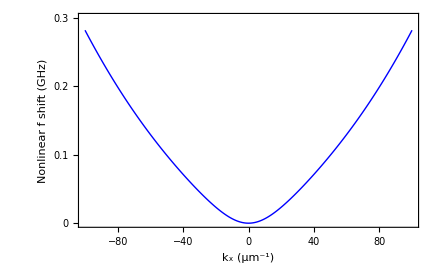

```mathematica
ListPlot[Table[{ky/10^6,freq2[0,0,ky]-(If[freqs2[LL,ky a,0,0.5][[1]]>0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]]) },{ky,-100 10^6,100 10^6,1 10^6}],Frame->True,FrameLabel->{"k_x (μm^-1)","Nonlinear f shift (GHz)"},PlotRange->{-0.0,0.3},LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->Directive[Blue,Thick],FrameStyle->Directive[Black,Thick],FrameTicks->{{ {0,0.1,0.2,0.3},{{0,""},{0.1,""},{0.2,""},{0.3,""}}},{Automatic,Automatic}}]
```

```mathematica
Table[{ky/10^6,(If[freqs2[LL,ky a,0,0.5][[1]]>0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]]) },{ky,-100 10^6,100 10^6,20 10^6}]
```

{{-100,19.4773},{-80,15.2935},{-60,11.6098},{-40,8.45701},{-20,6.04736},{0,5.04203},{20,6.04736},{40,8.45701},{60,11.6098},{80,15.2935},{100,19.4773}}

```mathematica
Table[{ky/10^6,(If[freqs2[LL,ky a,0,0.5][[1]]>0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]]) },{ky,-100 10^6,100 10^6,1 10^6}]
```

{{-100,19.4773},{-99,19.256},{-98,19.036},{-97,18.8173},{-96,18.5998},{-95,18.3837},{-94,18.1688},{-93,17.9552},{-92,17.7429},{-91,17.5319},{-90,17.3221},{-89,17.1136},{-88,16.9064},{-87,16.7004},{-86,16.4957},{-85,16.2922},{-84,16.0899},{-83,15.889},{-82,15.6892},{-81,15.4907},{-80,15.2935},{-79,15.0975},{-78,14.9027},{-77,14.7092},{-76,14.5169},{-75,14.3259},{-74,14.1361},{-73,13.9475},{-72,13.7602},{-71,13.5741},{-70,13.3892},{-69,13.2056},{-68,13.0233},{-67,12.8422},{-66,12.6623},{-65,12.4837},{-64,12.3064},{-63,12.1303},{-62,11.9555},{-61,11.782},{-60,11.6098},{-59,11.4388},{-58,11.2692},{-57,11.1009},{-56,10.9339},{-55,10.7683},{-54,10.604},{-53,10.4411},{-52,10.2795},{-51,10.1194},{-50,9.96067},{-49,9.80339},{-48,9.64757},{-47,9.49324},{-46,9.34043},{-45,9.18915},{-44,9.03944},{-43,8.89134},{-42,8.74488},{-41,8.60008},{-40,8.45701},{-39,8.31569},{-38,8.17617},{-37,8.03851},{-36,7.90275},{-35,7.76895},{-34,7.63717},{-33,7.50747},{-32,7.37991},{-31,7.25458},{-30,7.13155},{-29,7.01089},{-28,6.89269},{-27,6.77704},{-26,6.66403},{-25,6.55377},{-24,6.44635},{-23,6.34188},{-22,6.24049},{-21,6.14227},{-20,6.04736},{-19,5.95589},{-18,5.86797},{-17,5.78375},{-16,5.70335},{-15,5.62692},{-14,5.55459},{-13,5.4865},{-12,5.42279},{-11,5.36358},{-10,5.30902},{-9,5.25922},{-8,5.2143},{-7,5.17438},{-6,5.13957},{-5,5.10994},{-4,5.08558},{-3,5.06657},{-2,5.05295},{-1,5.04476},{0,5.04203},{1,5.04476},{2,5.05295},{3,5.06657},{4,5.08558},{5,5.10994},{6,5.13957},{7,5.17438},{8,5.2143},{9,5.25922},{10,5.30902},{11,5.36358},{12,5.42279},{13,5.4865},{14,5.55459},{15,5.62692},{16,5.70335},{17,5.78375},{18,5.86797},{19,5.95589},{20,6.04736},{21,6.14227},{22,6.24049},{23,6.34188},{24,6.44635},{25,6.55377},{26,6.66403},{27,6.77704},{28,6.89269},{29,7.01089},{30,7.13155},{31,7.25458},{32,7.37991},{33,7.50747},{34,7.63717},{35,7.76895},{36,7.90275},{37,8.03851},{38,8.17617},{39,8.31569},{40,8.45701},{41,8.60008},{42,8.74488},{43,8.89134},{44,9.03944},{45,9.18915},{46,9.34043},{47,9.49324},{48,9.64757},{49,9.80339},{50,9.96067},{51,10.1194},{52,10.2795},{53,10.4411},{54,10.604},{55,10.7683},{56,10.9339},{57,11.1009},{58,11.2692},{59,11.4388},{60,11.6098},{61,11.782},{62,11.9555},{63,12.1303},{64,12.3064},{65,12.4837},{66,12.6623},{67,12.8422},{68,13.0233},{69,13.2056},{70,13.3892},{71,13.5741},{72,13.7602},{73,13.9475},{74,14.1361},{75,14.3259},{76,14.5169},{77,14.7092},{78,14.9027},{79,15.0975},{80,15.2935},{81,15.4907},{82,15.6892},{83,15.889},{84,16.0899},{85,16.2922},{86,16.4957},{87,16.7004},{88,16.9064},{89,17.1136},{90,17.3221},{91,17.5319},{92,17.7429},{93,17.9552},{94,18.1688},{95,18.3837},{96,18.5998},{97,18.8173},{98,19.036},{99,19.256},{100,19.4773}}

```mathematica
If[freqs2[LL,100 10^6 a,0,0.5][[1]]>0,freqs2[LL,100 10^6 a,0,0.5][[1]],freqs2[LL,100 10^6 a,0,0.5][[2]]]
```

19.4773

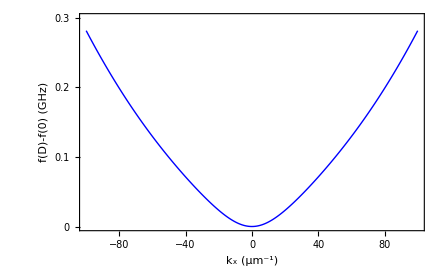

```mathematica
ListPlot[Table[{ky/10^6,freq2[0,0,ky]-(If[freqs2[LL,ky a,0,0.5][[1]]>0,freqs2[LL,ky a,0,0.5][[1]],freqs2[LL,ky a,0,0.5][[2]]]) },{ky,-100 10^6,100 10^6,1 10^6}],Frame->True,FrameLabel->{"k_x (μm^-1)","f(D)-f(0) (GHz)"},PlotRange->{-0.0,0.3},LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->Directive[Blue,Thick],FrameStyle->Directive[Black,Thick],FrameTicks->{{ {0,0.1,0.2,0.3},{{0,""},{0.1,""},{0.2,""},{0.3,""}}},{Automatic,Automatic}}]
```

## Compare D=0 and D=9 mJ/m^2 by running the code above for different values (Figure 6)

```mathematica
noDMI={{-100,19.75878357765944},{-99,19.532974592710392},{-98,19.308500517008397},{-97,19.08535737018533},{-96,18.863541225442447},{-95,18.643048215526438},{-94,18.42387453921615},{-93,18.206016467985794},{-92,17.98947035327304},{-91,17.774232634020226},{-90,17.56029984477575},{-89,17.347668624288907},{-88,17.13633572448506},{-87,16.926298020189666},{-86,16.717552519267517},{-85,16.51009637350796},{-84,16.30392689002657},{-83,16.099041543541055},{-82,15.895437989208645},{-81,15.693114076407454},{-80,15.492067863232023},{-79,15.292297631996744},{-78,15.093801905627323},{-77,14.896579465028646},{-76,14.70062936763712},{-75,14.505950967010852},{-74,14.31254393373827},{-73,14.12040827754878},{-72,13.929544370937023},{-71,13.739952974125021},{-70,13.55163526171352},{-69,13.364592850966627},{-68,13.178827831881474},{-67,12.994342799172923},{-66,12.811140886293959},{-65,12.62922580163269},{-64,12.448601866968731},{-63,12.26927405849747},{-62,12.091248050307446},{-61,11.914530260797335},{-60,11.739127901948489},{-59,11.565049031834475},{-58,11.392302610394173},{-57,11.220898558831669},{-56,11.050847822674195},{-55,10.882162439064851},{-54,10.7148556079215},{-53,10.548941767902553},{-52,10.384436676841956},{-51,10.221357497262554},{-50,10.059722887058822},{-49,9.899553095607438},{-48,9.74087006553618},{-47,9.583697540459973},{-46,9.428061178836819},{-45,9.273988673953776},{-44,9.12150988056523},{-43,8.970656947879853},{-42,8.821464459183362},{-41,8.673969577957829},{-40,8.528212200381278},{-39,8.38423511385139},{-38,8.242084161350997},{-37,8.101808410756764},{-36,7.963460328661204},{-35,7.827095957256425},{-34,7.692775093331897},{-33,7.5605614674849475},{-32,7.430522921464752},{-31,7.302731581318713},{-30,7.17726402304254},{-29,7.054201427303988},{-28,6.933629719095202},{-27,6.81563968699078},{-26,6.700327076879953},{-25,6.587792653356296},{-24,6.478142221725031},{-23,6.3714866025401875},{-22,6.2679415502453395},{-21,6.167627606374243},{-20,6.070669877699196},{-19,5.977197729458654},{-18,5.887344383900572},{-17,5.801246414870708},{-16,5.719043130082347},{-15,5.640875835035113},{-14,5.566886973435797},{-13,5.49721914394972},{-12,5.432013995046731},{-11,5.371411005418302},{-10,5.3155461616627155},{-9,5.26455055173968},{-8,5.2185488964523365},{-7,5.177658048903764},{-6,5.141985495171794},{-5,5.111627894788774},{-4,5.086669701107591},{-3,5.067181904182105},{-2,5.053220935383727},{-1,5.044827772096861},{0,5.0420272735124785},{1,5.044827772096861},{2,5.053220935383727},{3,5.067181904182105},{4,5.086669701107591},{5,5.111627894788774},{6,5.141985495171794},{7,5.177658048903764},{8,5.2185488964523365},{9,5.26455055173968},{10,5.3155461616627155},{11,5.371411005418302},{12,5.432013995046731},{13,5.49721914394972},{14,5.566886973435797},{15,5.640875835035113},{16,5.719043130082347},{17,5.801246414870708},{18,5.887344383900572},{19,5.977197729458654},{20,6.070669877699196},{21,6.167627606374243},{22,6.2679415502453395},{23,6.3714866025401875},{24,6.478142221725031},{25,6.587792653356296},{26,6.700327076879953},{27,6.81563968699078},{28,6.933629719095202},{29,7.054201427303988},{30,7.17726402304254},{31,7.302731581318713},{32,7.430522921464752},{33,7.5605614674849475},{34,7.692775093331897},{35,7.827095957256425},{36,7.963460328661204},{37,8.101808410756764},{38,8.242084161350997},{39,8.38423511385139},{40,8.528212200381278},{41,8.673969577957829},{42,8.821464459183362},{43,8.970656947879853},{44,9.12150988056523},{45,9.273988673953776},{46,9.428061178836819},{47,9.583697540459973},{48,9.74087006553618},{49,9.899553095607438},{50,10.059722887058822},{51,10.221357497262554},{52,10.384436676841956},{53,10.548941767902553},{54,10.7148556079215},{55,10.882162439064851},{56,11.050847822674195},{57,11.220898558831669},{58,11.392302610394173},{59,11.565049031834475},{60,11.739127901948489},{61,11.914530260797335},{62,12.091248050307446},{63,12.26927405849747},{64,12.448601866968731},{65,12.62922580163269},{66,12.811140886293959},{67,12.994342799172923},{68,13.178827831881474},{69,13.364592850966627},{70,13.55163526171352},{71,13.739952974125021},{72,13.929544370937023},{73,14.12040827754878},{74,14.31254393373827},{75,14.505950967010852},{76,14.70062936763712},{77,14.896579465028646},{78,15.093801905627323},{79,15.292297631996744},{80,15.492067863232023},{81,15.693114076407454},{82,15.895437989208645},{83,16.099041543541055},{84,16.30392689002657},{85,16.51009637350796},{86,16.717552519267517},{87,16.926298020189666},{88,17.13633572448506},{89,17.347668624288907},{90,17.56029984477575},{91,17.774232634020226},{92,17.98947035327304},{93,18.206016467985794},{94,18.42387453921615},{95,18.643048215526438},{96,18.863541225442447},{97,19.08535737018533},{98,19.308500517008397},{99,19.532974592710392},{100,19.75878357765944}};
```

```mathematica
withDMI={{-100,19.477273763834027},{-99,19.25597283806029},{-98,19.035967438951428},{-97,18.817253800467753},{-96,18.599828214697908},{-95,18.38368703799164},{-94,18.16882669741026},{-93,17.95524369748077},{-92,17.742934627502237},{-91,17.531896169145142},{-90,17.322125104594527},{-89,17.113618325134812},{-88,16.906372840248803},{-87,16.700385787302967},{-86,16.495654441727385},{-85,16.292176227933684},{-84,16.089948730726704},{-83,15.888969707575503},{-82,15.689237101476808},{-81,15.490749054719906},{-80,15.293503923325503},{-79,15.09750029261959},{-78,14.902736993433695},{-77,14.70921311958675},{-76,14.516928046254344},{-75,14.325881449524472},{-74,14.136073327198757},{-73,13.94750402080136},{-72,13.760174238995791},{-71,13.574085082522721},{-70,13.389238070473628},{-69,13.205635168494709},{-68,13.023278818594008},{-67,12.842171970733652},{-66,12.662318116613978},{-65,12.483721325475477},{-64,12.30638628210079},{-63,12.130318327369006},{-62,11.955523501165478},{-61,11.782008588213145},{-60,11.609781166646258},{-59,11.438849659678242},{-58,11.269223390592598},{-57,11.100912641054617},{-56,10.933928713155227},{-55,10.768283995401367},{-54,10.603992032491025},{-53,10.441067599763143},{-52,10.27952678188849},{-51,10.119387056430377},{-50,9.960667382405498},{-49,9.803388293931839},{-48,9.647571999375034},{-47,9.493242486111937},{-46,9.340425630989275},{-45,9.189149316756474},{-44,9.039443554510274},{-43,8.891340612192476},{-42,8.744875149258846},{-41,8.6000843572322},{-40,8.457008106089855},{-39,8.31568909612232},{-38,8.176173014949853},{-37,8.038508698744726},{-36,7.902748297225782},{-35,7.768947441061122},{-34,7.637165410406792},{-33,7.507465302998676},{-32,7.379914199412422},{-31,7.254583323518251},{-30,7.131548194361457},{-29,7.010888766854634},{-28,6.892689556455744},{-27,6.777039743183892},{-26,6.66403324997111},{-25,6.553768788656787},{-24,6.446349867048035},{-23,6.341884749457716},{-22,6.240486362715283},{-21,6.142272138670192},{-20,6.047363784671884},{-19,5.955886972408953},{-18,5.8679709367292725},{-17,5.783747975754686},{-16,5.703352845361815},{-15,5.6269220423442246},{-14,5.554592972538089},{-13,5.4865030042254475},{-12,5.422788409091455},{-11,5.36358319851816},{-10,5.309017866711077},{-9,5.259218058304933},{-8,5.214303181907349},{-7,5.174384997284665},{-6,5.139566207500088},{-5,5.109939091726526},{-4,5.085584215315156},{-3,5.066569256677391},{-2,5.052947986633422},{-1,5.044759435135324},{0,5.0420272735124785},{1,5.0447594351353215},{2,5.052947986633421},{3,5.066569256677387},{4,5.085584215315162},{5,5.109939091726535},{6,5.139566207500089},{7,5.174384997284667},{8,5.214303181907349},{9,5.259218058304924},{10,5.309017866711072},{11,5.363583198518146},{12,5.422788409091446},{13,5.486503004225459},{14,5.5545929725381145},{15,5.626922042344217},{16,5.70335284536183},{17,5.783747975754682},{18,5.867970936729246},{19,5.955886972408973},{20,6.047363784671867},{21,6.1422721386702275},{22,6.2404863627152745},{23,6.341884749457752},{24,6.446349867048068},{25,6.553768788656831},{26,6.6640332499712205},{27,6.777039743183857},{28,6.892689556455682},{29,7.010888766854644},{30,7.131548194361413},{31,7.254583323518197},{32,7.379914199412447},{33,7.507465302998668},{34,7.637165410406746},{35,7.768947441061151},{36,7.902748297225752},{37,8.038508698744705},{38,8.176173014949828},{39,8.315689096122288},{40,8.457008106089841},{41,8.600084357232221},{42,8.744875149258869},{43,8.891340612192499},{44,9.039443554510369},{45,9.189149316756454},{46,9.340425630989253},{47,9.493242486111882},{48,9.647571999375073},{49,9.803388293931814},{50,9.960667382405562},{51,10.119387056430448},{52,10.279526781888547},{53,10.441067599763203},{54,10.603992032490906},{55,10.768283995401456},{56,10.933928713155334},{57,11.100912641054645},{58,11.269223390592595},{59,11.438849659678255},{60,11.609781166646052},{61,11.782008588213145},{62,11.955523501165464},{63,12.130318327368943},{64,12.306386282100886},{65,12.483721325475514},{66,12.662318116613953},{67,12.842171970733572},{68,13.023278818593946},{69,13.20563516849472},{70,13.389238070473782},{71,13.574085082522686},{72,13.76017423899586},{73,13.94750402080139},{74,14.136073327198817},{75,14.325881449524587},{76,14.516928046254232},{77,14.709213119586806},{78,14.902736993433773},{79,15.097500292619706},{80,15.293503923325467},{81,15.49074905471982},{82,15.689237101477099},{83,15.88896970757543},{84,16.089948730726537},{85,16.292176227933687},{86,16.495654441727368},{87,16.700385787302995},{88,16.906372840248945},{89,17.11361832513484},{90,17.322125104594534},{91,17.531896169145107},{92,17.742934627502},{93,17.955243697480814},{94,18.168826697410168},{95,18.383687037991766},{96,18.59982821469796},{97,18.817253800467704},{98,19.03596743895165},{99,19.255972838060284},{100,19.477273763834056}};
```

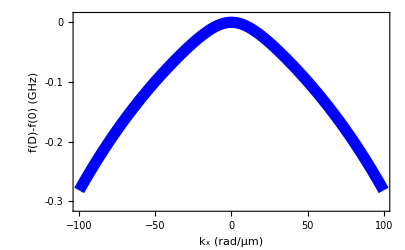

```mathematica
ListPlot[Table[{withDMI[[i]][[1]],withDMI[[i]][[2]]-noDMI[[i]][[2]]},{i,1,Length[noDMI]}],Frame->True,FrameLabel->{"k_x (rad/μm)","f(D)-f(0) (GHz)"},PlotRange->{-0.31,0.01},LabelStyle->Directive[Large,Black, Bold,FontFamily->Times],Joined->True,PlotStyle->Directive[Blue,Thickness[0.02]],FrameStyle->Directive[Black,Thick],FrameTicks->{{ {0,-0.1,-0.2,-0.3},{{0,""},{-0.1,""},{-0.2,""},{-0.3,""}}},{Automatic,Automatic}}]
```